```mathematica
dataDSi=Import["D:\\Specific Heat of Degenerate Silicon.DAT"]
```

{{1.27,0.089},{1.98,0.167},{2.32,0.218},{3.08,0.401},{3.5,0.528},{4.17,0.788}}

```mathematica
lm=LinearModelFit[dataDSi,{T,T^3},T,IncludeConstantBasis->False]
```

FittedModel[0.0552057 T+0.0077302 T^3]

```mathematica
datLnDSi=Table[{dataDSi[[i]][[1]]^2,dataDSi[[i]][[2]]/dataDSi[[i]][[1]]},{i,dataDSi//Length}]
```

{{1.6129,0.0700787},{3.9204,0.0843434},{5.3824,0.0939655},{9.4864,0.130195},{12.25,0.150857},{17.3889,0.188969}}

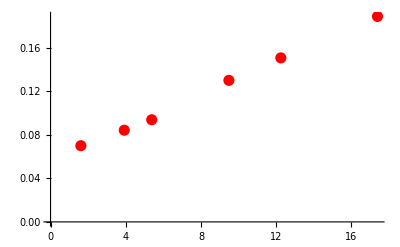

```mathematica
p0=ListPlot[datLnDSi,PlotStyle->{Red,PointSize[0.02]}]
```

```mathematica
lm=LinearModelFit[datLnDSi,{x},x]
```

FittedModel[0.0554041+0.00771335 x]

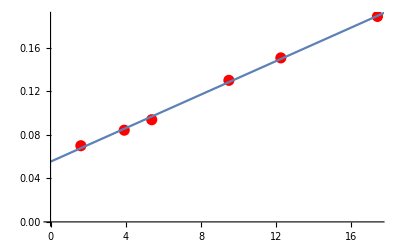

```mathematica
pl=Plot[lm[x],{x,0,20}];
Show[p0,pl]
```

```mathematica
lm["BestFit"]
```

0.0554041+0.00771335 x

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.0102344 | 0.0102344 | 2123.54 | 1.32638×10^-6
Error | 4 | 0.000019278 | 4.81951×10^-6 |  | 
Total | 5 | 0.0102537 |  |  |

```mathematica
lm["RSquared"]
```

0.99812

```mathematica
nlm=NonlinearModelFit[dataDSi,{γ*T+α*T^3},{γ,α},T]
```

FittedModel[0.0552057 T+0.0077302 T^3]

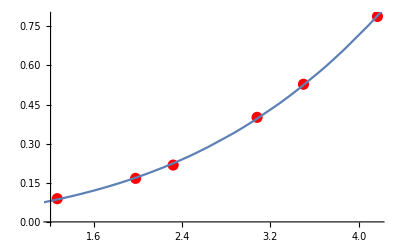

```mathematica
Show[ListPlot[dataDSi,PlotStyle->{Red,PointSize[0.02]}],Plot[nlm[x],{x,0,20}]]
```

```mathematica
nlm["BestFit"]
```

0.0552057 T+0.0077302 T^3

```mathematica
nlm["ANOVATable"]
```

| DF | SS | MS
Model | 2 | 1.14376 | 0.57188
Error | 4 | 0.000103068 | 0.0000257669
Uncorrected Total | 6 | 1.14386 | 
Corrected Total | 5 | 0.343783 |

```mathematica
nlm["RSquared"]
```

0.99991